## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs4=GenAll[4];Length[baseGraphs4]
```

127

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 4 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations4=CompleteRelations[baseGraphs4];Length[withRelations4]
```

127

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 14 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations4[k,"graph"],k],{k,Take[Keys[withRelations4],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs4=Select[Reverse[Keys[withRelations4]],CompleteGraphQ[withRelations4[#,"graph"]]&];Length[completeGraphs4]
```

15

```mathematica
baseGraphAxioma4=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations4[k,"vertexsets"]],{k,completeGraphs4}]]
```

{x728→v1234,x697→v123x4,x637→v124x3,x608→v12x34,x607→v12x3x4,x473→v134x2,x448→v13x24,x445→v13x2x4,x400→v14x23,x391→v14x2x3,x377→v1x234,x373→v1x23x4,x367→v1x24x3,x365→v1x2x34,x364→v1x2x3x4}

Now we get some lists of variables

```mathematica
allGraphVariables4=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations4]}];Length[allGraphVariables4]
```

127

```mathematica
baseGraphAxioma4Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma4]]]];Length[baseGraphAxioma4Vars]
```

15

```mathematica
baseKeys4=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma4]
```

{728,697,637,608,607,473,448,445,400,391,377,373,367,365,364}

```mathematica
Take[baseGraphAxioma4Vars,4]
```

{v1234,v123x4,v124x3,v12x34}

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations4[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma4],
{key,baseKeys4}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 42 base variables.
This procedure only works fior the b01... variables since we need 4 vertices for the current implementation

```mathematica
withColorTables4=withRelations4;
```

```mathematica
GenerateColorTable4[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[4],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable4[withColorTables4,2]
```

{{x2y1z2,-x2y1z2+Missing[KeyAbsent,colofour]},{x2y1z3,-x2y1z3+Missing[KeyAbsent,colofour]},{x2y1z4,-x2y1z4+Missing[KeyAbsent,colofour]},{x2y2z3,-x2y2z3+Missing[KeyAbsent,colofour]},{x2y2z4,-x2y2z4+Missing[KeyAbsent,colofour]},{Missing[KeyAbsent,colofour],0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys4=baseKeys4;
```

```mathematica
baseGraphAxioma4Vars
```

{v1234,v123x4,v124x3,v12x34,v12x3x4,v134x2,v13x24,v13x2x4,v14x23,v14x2x3,v1x234,v1x23x4,v1x24x3,v1x2x34,v1x2x3x4}

```mathematica
Monitor[Table[
withColorTables4[k]["colortable"]=GenerateColorTable4[withColorTables4,k]
,
{k,baseGraphKeys4}
],k];
```

```mathematica
Keys[withColorTables4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable4[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables4[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables4[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables4[r1],"colortable"],
withColorTables4[r1,"colortable"]=TryComputeColourTable4[r1],
];
If[!KeyExistsQ[withColorTables4[r2],"colortable"],
withColorTables4[r2,"colortable"]=TryComputeColourTable4[r2],

];
withColorTables4[k,"colortable"]=withColorTables4[r1,"colortable"]+withColorTables4[r2,"colortable"];
withColorTables4[k,"colofour"]=withColorTables4[r1,"colofour"]+withColorTables4[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables4[k]["relations"]}
]
];
withColorTables4[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables4[0],"colortable"]
```

False

```mathematica
TryComputeColourTable4[0];
```

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables4[k]["colortable2"]=withColorTables4[k]["colortable"]
,
{k,Keys[withColorTables4]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp4=withColorTables4;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp4[k,"comp"]=GreaterEqual;withComp4[k,"compwhy"]="No IH";k,{k,Keys[withComp4]}]//Length
```

127

```mathematica
CosyPrint4[key_,assoc_:withComp4, colofour_:"colofour"]:=With[
{current=assoc[key]},
Framed[
Labeled[
Graph[current["graph"],ImageSize->{100,100}],
{Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current[colofour]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},ColourForKey[assoc,key]],
current["compwhy"]
},

{Bottom,Top}]]
]
```

```mathematica
ColofourPrint4[key_]:=With[
{current=withComp4[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{70,70}]
}
],
{Style[current["signature"],First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]->TraditionalForm[current["colofour"]],ChromaticPolynomial[current["graph"],4]/24}]]]
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right],
 result=current},
(*Print[currentS,"  ", leftS, "  ", rightS];*)
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
]
];
result
]
```

```mathematica
RecalculateComp4[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current,newValue},
current=withComp4[k];
If[depth<maxdepth && ! current["marked"],
withComp4[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];


withComp4[r1,"parents"]=Append[withComp4[r1,"parents"],k];
withComp4[r2,"parents"]=Append[withComp4[r2,"parents"],k];
withComp4[k,"children"]=Append[withComp4[k,"children"],{r1,r2}];

RecalculateComp4[r1,depth+1,maxdepth];
RecalculateComp4[r2,depth+1,maxdepth];
newValue=MayBeReassign[k,withComp4[k,"comp"], withComp4[r1,"comp"],withComp4[r2,"comp"]];
If[ToString[withComp4[k,"comp"]]≠ToString[newValue],
Print[k," becomes ", newValue];
withComp4[k,"comp"]=newValue;
withComp4[k,"compwhy"]= "Since " <> ToString[r]<> " and " <> ToString[r1]<> " is " <>  ToString[withComp4[r1,"comp"]] <> " and " <> ToString[r2]<> " is " <>  ToString[withComp4[r2,"comp"]]
];
];
]
,{r,withComp4[k]["relations"]}
];
];withComp4[k,"comp"]
]
```

```mathematica
Table[withComp4[k,"marked"]=False;withComp4[k,"parents"]={};withComp4[k,"children"]={};k,{k,Keys[withComp4]}];markCount=0
```

0

```mathematica
IsPlanarSet[set_,total_]:=Block[{result,sot=set-1,breaks=0,i,previous},
If[Length[set]==1,
result=True,
For[i=2,i≤Length[sot],i++,
If[Mod[sot[[i-1]]+1,total]≠Mod[sot[[i]],total],
breaks++;
]
];
If[Mod[sot[[Length[sot]]]+1,total]≠Mod[sot[[1]],total],
breaks++;
];
result=breaks<2;
];
result
]
```

```mathematica
IsPlanarContraction[assoc_,key_]:=Block[{total},
total=Length[Flatten[assoc[key,"vertexsets"]]];
Fold[And,Table[IsPlanarSet[s,total],{s,assoc[key,"vertexsets"]}]]
];
```

```mathematica
Monitor[Table[If[
MyPlanar[withComp4,k],
withComp4[k,"comp"]=Greater;
withComp4[k,"compwhy"]="Planar contraction";
1,
0]
,{k,baseKeys4}],k]
```

{1,1,1,1,1,1,0,0,1,1,1,1,0,1,0}

```mathematica
Table[withComp4[k,"comp"]=Equal;withComp4[k,"compwhy"]="Contains K Five";k,{k,Select[baseKeys4,!PlanarGraphQ[withComp4[#,"graph"]]&]}]//Length
```

0

```mathematica
(*Monitor[
Table[If[
PlanarGraphQ[EmbedGraph4[withComp4,key]],
Print[key, " is planar and follows IH "];
withComp4[key]["compwhy"]="Embedding is planar and follows IH (Plantri 10000)";
withComp4[key]["comp"]=Greater;
1,
0
],{key,Keys[withComp4]}],
key]//Total*)
```

```mathematica
markCount=0
```

0

```mathematica
Monitor[RecalculateComp4[0,0,20],markCount]
```

363 becomes Greater

360 becomes Greater

369 becomes Greater

351 becomes Greater

354 becomes Greater

355 becomes Greater

357 becomes Greater

352 becomes Greater

353 becomes Greater

382 becomes Greater

324 becomes Greater

333 becomes Greater

336 becomes Greater

337 becomes Greater

334 becomes Greater

342 becomes Greater

346 becomes Greater

327 becomes Greater

328 becomes Greater

325 becomes Greater

417 becomes Greater

414 becomes Greater

243 becomes Greater

270 becomes Greater

279 becomes Greater

282 becomes Greater

273 becomes Greater

274 becomes Greater

276 becomes Greater

271 becomes Greater

309 becomes Greater

300 becomes Greater

252 becomes Greater

255 becomes Greater

256 becomes Greater

257 becomes Greater

253 becomes Greater

246 becomes Greater

247 becomes Greater

244 becomes Greater

245 becomes Greater

577 becomes Greater

487 becomes Greater

517 becomes Greater

488 becomes Greater

486 becomes Greater

576 becomes Greater

606 becomes Greater

666 becomes Greater

516 becomes Greater

546 becomes Greater

0 becomes Greater

165 becomes Greater

193 becomes Greater

168 becomes Greater

162 becomes Greater

190 becomes Greater

218 becomes Greater

81 becomes Greater

108 becomes Greater

117 becomes Greater

120 becomes Greater

121 becomes Greater

122 becomes Greater

118 becomes Greater

111 becomes Greater

112 becomes Greater

109 becomes Greater

110 becomes Greater

145 becomes Greater

136 becomes Greater

90 becomes Greater

93 becomes Greater

94 becomes Greater

97 becomes Greater

91 becomes Greater

84 becomes Greater

85 becomes Greater

87 becomes Greater

82 becomes Greater

27 becomes Greater

36 becomes Greater

39 becomes Greater

40 becomes Greater

37 becomes Greater

45 becomes Greater

49 becomes Greater

30 becomes Greater

31 becomes Greater

28 becomes Greater

63 becomes Greater

72 becomes Greater

54 becomes Greater

18 becomes Greater

22 becomes Greater

26 becomes Greater

9 becomes Greater

12 becomes Greater

13 becomes Greater

14 becomes Greater

16 becomes Greater

10 becomes Greater

3 becomes Greater

4 becomes Greater

6 becomes Greater

1 becomes Greater

2 becomes Greater

Greater

Now we have a look at some graphs that might have been forgotten:

```mathematica
Monitor[Table[If[
MyPlanar[withComp4,k],
Print[k, " is a planar contraction"];
withComp4[k,"comp"]=Greater;
withComp4[k,"compwhy"]="Planar contraction (late)";
1,
0]
,{k,Select[Keys[withComp4],ToString[withComp4[#,"comp"]]=="GreaterEqual"&]}],k]//Total
```

280 is a planar contraction

283 is a planar contraction

286 is a planar contraction

361 is a planar contraction

442 is a planar contraction

5

```mathematica
Select[Keys[withComp4],withComp4[#,"comp"]==Greater&]//Length
```

123

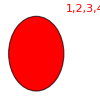
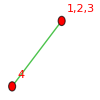
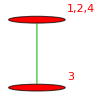
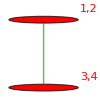
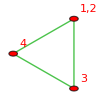
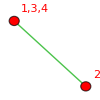
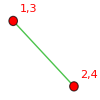
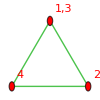
{-Graphics-{728→v1234,1/6}Planar contraction,-Graphics-{697→v123x4,1/2}Planar contraction,-Graphics-{637→v124x3,1/2}Planar contraction,-Graphics-{608→v12x34,1/2}Planar contraction,-Graphics-{607→v12x3x4,1}Planar contraction,-Graphics-{473→v134x2,1/2}Planar contraction,-Graphics-{448→v13x24,1/2}No IH,-Graphics-{445→v13x2x4,1}No IH,-Graphics-{400→v14x23,1/2}Planar contraction,-Graphics-{391→v14x2x3,1}Planar contraction,-Graphics-{377→v1x234,1/2}Planar contraction,-Graphics-{373→v1x23x4,1}Planar contraction,-Graphics-{367→v1x24x3,1}No IH,-Graphics-{365→v1x2x34,1}Planar contraction,-Graphics-{364→v1x2x3x4,1}No IH}

```mathematica
Table[CosyPrint4[k,withComp4],{k,baseKeys4}]
```

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm4=withComp4;
```

```mathematica
Keys[stubbornForm4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,compwhy,marked,parents,children}

```mathematica
stubbornKeys4 = Select[Keys[stubbornForm4],(ToString[stubbornForm4[#]["comp"]]=="GreaterEqual")&];Length[stubbornKeys4]
```

4

```mathematica
334
```

334

```mathematica
Intersection[baseKeys4,stubbornKeys4]//Length
```

4

```mathematica
CosyPrintThree4[key_]:=ColorTablePrint[key,stubbornForm4,"colofour","colortable"]
```

```mathematica
ineqsthree4=Monitor[Table[stubbornForm4[k]["comp"][stubbornForm4[k]["colofour"],0],{k,Keys[stubbornForm4]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsthree4]
```

127

```mathematica
1894
```

1894

```mathematica
ineqsthree42=Fold[And,ineqsthree4]//Simplify
```

v1234>0&&v123x4>0&&v124x3>0&&v12x34>0&&v12x3x4>0&&v134x2>0&&v13x24≥0&&v13x2x4≥0&&v14x23>0&&v14x2x3>0&&v1x234>0&&v1x23x4>0&&v1x24x3≥0&&v1x2x34>0&&v1x2x3x4≥0&&v13x2x4+v1x2x3x4>0&&v13x24+v1x24x3>0&&v1x24x3+v1x2x3x4>0&&v13x24+v13x2x4>0

```mathematica
ExpressionToTable[ineqsthree42]
```

v1x234>0
v1234>0
v14x2x3>0
v13x2x4≥0
v1x2x3x4≥0
v1x23x4>0
v12x3x4>0
v123x4>0
v134x2>0
v1x24x3≥0
v124x3>0
v14x23>0
v13x24≥0
v1x2x34>0
v12x34>0
v13x2x4+v1x2x3x4>0
v13x24+v13x2x4>0
v1x24x3+v1x2x3x4>0
v13x24+v1x24x3>0

```mathematica
repcolofour4base=Table[stubbornForm4[k,"colofour"]->Labeled[stubbornForm4[k,"graph"],Style[stubbornForm4[k,"colofour"],ColourForKey[stubbornForm4,k],If[MemberQ[{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key},k],{FontFamily->"Consolas", Italic,Bold,Underlined,20},Plain]]],{k,baseKeys4}];
```

```mathematica
repcolofour4=Table[stubbornForm4[k,"colofour"]->stubbornForm4[k,"graph"],{k,Keys[stubbornForm4]}];
```

```mathematica
Take[ineqsthree42,3]
```

v1234>0&&v123x4>0&&v124x3>0

```mathematica
ExpressionToTable[Reduce[ineqsthree42]]/.repcolofour4base
```

-Graphics-v1x234>0
-Graphics-v1234>0
-Graphics-v14x2x3>0
-Graphics-v1x23x4>0
-Graphics-v12x3x4>0
-Graphics-v123x4>0
-Graphics-v134x2>0
-Graphics-v124x3>0
-Graphics-v14x23>0
-Graphics-v1x2x34>0
-Graphics-v12x34>0
(-Graphics-v13x24>0&&-Graphics-v1x2x3x4>0&&((-Graphics-v13x2x4==0&&-Graphics-v1x24x3>0)||(-Graphics-v1x24x3==0&&-Graphics-v13x2x4≥0)))||(-Graphics-v13x24≥0&&-Graphics-v1x2x3x4≥0&&-Graphics-v13x2x4>0&&-Graphics-v1x24x3>0)

```mathematica
(*Reduce[ineqsthree42&&(v14x23x4==0)&&(v13x2x44==0)&&(v14x24x3==0)&&(v12x34x4==0)&&(v1x24x34==0)]*)
```

```mathematica
ExpressionToTable[ineqsthree42]/.repcolofour4base
```

-Graphics-v1x234>0
-Graphics-v1234>0
-Graphics-v14x2x3>0
-Graphics-v13x2x4≥0
-Graphics-v1x2x3x4≥0
-Graphics-v1x23x4>0
-Graphics-v12x3x4>0
-Graphics-v123x4>0
-Graphics-v134x2>0
-Graphics-v1x24x3≥0
-Graphics-v124x3>0
-Graphics-v14x23>0
-Graphics-v13x24≥0
-Graphics-v1x2x34>0
-Graphics-v12x34>0
-Graphics-v13x2x4+-Graphics-v1x2x3x4>0
-Graphics-v13x24+-Graphics-v13x2x4>0
-Graphics-v1x24x3+-Graphics-v1x2x3x4>0
-Graphics-v13x24+-Graphics-v1x24x3>0

```mathematica
baseGraphics4Rep=Map[stubbornForm4[#,"colofour"]->Labeled[Graph[stubbornForm4[#,"graph"],EdgeStyle->
ColourForKey[stubbornForm4,#]],Style[#,ColourForKey[stubbornForm4,#]]]&,baseKeys4]
```

{v1234→-Graphics-728,v123x4→-Graphics-697,v124x3→-Graphics-637,v12x34→-Graphics-608,v12x3x4→-Graphics-607,v134x2→-Graphics-473,v13x24→-Graphics-448,v13x2x4→-Graphics-445,v14x23→-Graphics-400,v14x2x3→-Graphics-391,v1x234→-Graphics-377,v1x23x4→-Graphics-373,v1x24x3→-Graphics-367,v1x2x34→-Graphics-365,v1x2x3x4→-Graphics-364}

## Find the tree base

```mathematica
treeForm4=stubbornForm4;
```

First we get the keys of everything which is a tree.

```mathematica
treeKeys4=Select[Keys[treeForm4],With[{g=treeForm4[#,"graph"]},TreeGraphQ[g]]&];Length[treeKeys4]
```

42

Ensure that they use all the variables in their colofour

```mathematica
Flatten[Table[ListofVars[treeForm4[ k,"colofour"]],{k,treeKeys4}]]//DeleteDuplicates//Length
```

15

Now we compose a set of equations.one for each tree.  We define new variables for the trees.

```mathematica
treeEquations4=Table[Symbol["t"<>ToString[k]]==treeForm4[k,"colofour"],{k,treeKeys4}];Length[treeEquations4]
```

42

We now reduce them to the atom variables.  Since there are too many trees, some trees will be defined as a function of other trees

```mathematica
reducedTreeEquations4= Reduce[treeEquations4,baseGraphAxioma4Vars];Length[reducedTreeEquations4]
```

42

```mathematica
reducedTreeEquationsList4=Table[reducedTreeEquations4[[k]],{k,Length[reducedTreeEquations4]}];
```

we filter out equations that are “tree” only, which means they don’t contain any of the base axioms

```mathematica
reducedTreeEquationsList4Base=Select[reducedTreeEquationsList4,Intersection[ListofVars[#],baseGraphAxioma4Vars]≠{}&];Length[reducedTreeEquationsList4Base]
```

15

```mathematica
treeVars4=Select[ListofVars[reducedTreeEquationsList4Base]//DeleteDuplicates//Sort,StringStartsQ[SymbolName[#],"t"]&];Take[treeVars4,4]
```

{t377,t39,t442,t448}

```mathematica
treeKeys4=Map[SymbolToKey,treeVars4];Length[treeKeys4]
```

15

```mathematica
Table[treeForm4[k,"comp"],{k,treeKeys4}]//Tally
```

{{Greater,14},{GreaterEqual,1}}

```mathematica
Monitor[Table[MyPlanar[treeForm4,k],{k,treeKeys4}],k]//Tally
```

{{True,11},{False,4}}

Compute the matrix of the tree transformation

```mathematica
repTree4=Map[#[[1]]->#[[2]]&,reducedTreeEquationsList4Base];Take[repTree4,4]
```

{v1234→t728,v123x4→t697,v124x3→t637,v12x34→t608}

```mathematica
Monitor[Table[
treeForm4[k,"colofourtree"]=Simplify[(treeForm4[k,"colofour"]/.repTree4)];
treeForm4[k,"colortabletree"]=Simplify[(treeForm4[k,"colortable"]/.repTree4)]
,{k,Keys[treeForm4]}],k];
```

```mathematica
repTreeGraphics4=Table[treeForm4[k,"colofourtree"]->Labeled[treeForm4[k,"graph"],Style[k,ColourForKey[treeForm4,k]]],{k,treeKeys4}];
```

```mathematica
matTree4=CoefficientArrays[Map[#[[2]]&,repTree4],treeVars4][[2]];
```

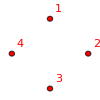
-Graphics-{0→t377+t442+t473+t697+t728+t85-t91+t93+2 t97,32/3}Since x0 == x243 + x486 and 243 is Greater and 486 is Greater

```mathematica
CosyPrint4[0,treeForm4,"colofourtree"]
```

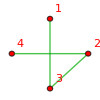
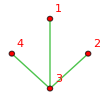
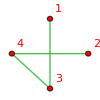
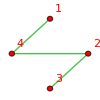
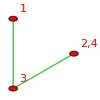
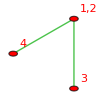
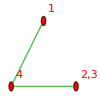
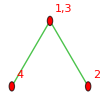
{-Graphics-{93→t93,9/2}Since x93 == x336 + x606 and 336 is Greater and 606 is Greater,-Graphics-{91→t91,9/2}Since x91 == x334 + x577 and 334 is Greater and 577 is Greater,-Graphics-{85→t85,9/2}Since x85 == x328 + x607 and 328 is Greater and 607 is Greater,-Graphics-{39→t39,9/2}Since x39 == x282 + x606 and 282 is Greater and 606 is Greater,-Graphics-{97→t97,3/2}Since x97 == x367 + x637 and 367 is GreaterEqual and 637 is Greater,-Graphics-{606→t606,3/2}Since x606 == x607 + x608 and 607 is Greater and 608 is Greater,-Graphics-{49→t49,3/2}Since x49 == x373 + x697 and 373 is Greater and 697 is Greater,-Graphics-{442→t442,3/2}Planar contraction (late),-Graphics-{697→t697,1/2}Planar contraction,-Graphics-{637→t637,1/2}Planar contraction,-Graphics-{608→t608,1/2}Planar contraction,-Graphics-{473→t473,1/2}Planar contraction,-Graphics-{448→t448,1/2}No IH,-Graphics-{377→t377,1/2}Planar contraction,-Graphics-{728→t728,1/6}Planar contraction}

```mathematica
Table[CosyPrint4[k,treeForm4,"colofourtree"],{k,Sort[treeKeys4,VertexCount[treeForm4[#1,"graph"]]>VertexCount[treeForm4[#2,"graph"]]&]}]
```

```mathematica
stubbornKeys4 = Select[Keys[treeForm4],(ToString[treeForm4[#]["comp"]]=="GreaterEqual")&];Length[treeForm4];Length[stubbornKeys4]
```

4

## Now define full

```mathematica
fiveNodes=treeForm4;
```

```mathematica
DefineFull4[]:=Block[{empty = fiveNodes[lambdaKey4],amigo1=fiveNodes[alfaKey4], amigo2=fiveNodes[betaKey4], newEntry, fivePositions},
fivePositions=Append[N[MyCircle[{{1},{2},{3},{4}},4]],{0,0}];
newEntry=Association[];
newEntry["signature"]="full";
Table[
newEntry[key]=Simplify[2*empty[key]-(amigo1[key]+amigo2[key])]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["compwhy"]="This is to be proven";
newEntry["matrix"]=empty["matrix"];
newEntry["graph"]=Graph[{1<->2,2<->3,3<->4,4<->1,5<->1,5<->2,5<->3,5<->4},VertexLabels->"Name",VertexSize->Normal,
ImageSize->{50,50},VertexCoordinates->fivePositions];
newEntry["vertexsets"]=empty["vertexsets"];
newEntry["vertices"]=empty["vertices"];
newEntry["relations"]={};
newEntry
]
```

```mathematica
fiveNodes["full"]=DefineFull4[];
```

```mathematica
fiveNodes[alfaKey4,"colofour"]/.repcolofour4base
```

-Graphics-v13x2x4+-Graphics-v1x2x3x4

```mathematica
fiveNodes[betaKey4,"colofour"]/.repcolofour4base
```

-Graphics-v1x24x3+-Graphics-v1x2x3x4

```mathematica
fiveNodes[lambdaKey4,"colofour"]/.repcolofour4base
```

-Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4+-Graphics-v1x2x3x4

```mathematica
ColorTablePrint["full",fiveNodes,"colofour","colortable"]/.graphicsthree
```

-Graphics-full2 -Graphics-+-Graphics-+-Graphics-GreaterEqual
( | = | ≠
1<->2 | 0 | 2 -Graphics-+-Graphics-+-Graphics-
1<->3 | 2 -Graphics-+-Graphics- | -Graphics-
1<->4 | 0 | 2 -Graphics-+-Graphics-+-Graphics-
2<->3 | 0 | 2 -Graphics-+-Graphics-+-Graphics-
2<->4 | 2 -Graphics-+-Graphics- | -Graphics-
3<->4 | 0 | 2 -Graphics-+-Graphics-+-Graphics-)

## For all we have not nailed yet, we set their colofour to zero and combine them with the inequalities

```mathematica
TryZeroFor4[key_]:=Block[{current=fiveNodes[key]},
If[ToString[Reduce[current["colofour"]==0&&ineqsthree42]]=="False",
current["comp"]=Greater;
current["compwhy"]="Would be inconsistent with other inequalities";
fiveNodes[key]=current;
Print[key, " becomes Greater because of inequalities"];
1,
0
]
]
```

```mathematica
stillAProblem4=Select[Keys[fiveNodes],ToString[fiveNodes[#,"comp"]]=="GreaterEqual"&];Length[stillAProblem4]
```

5

```mathematica
Monitor[Table[TryZeroFor4[k],{k,Select[Keys[fiveNodes],!NumberQ[#]&]}],{k}]//Total
```

full becomes Greater because of inequalities

1

```mathematica
TryZeroFor4["full"]
```

0

```mathematica
GetCompTreeForm[key_]:=Block[{},treeForm4[key]]
```

```mathematica
SetCompTreeForm[key_,value_]:=Block[{},treeForm4[key]=value]
```

```mathematica
PropagateComp[GetCompTreeForm,SetCompTreeForm,Keys[treeForm4]]
```

0

```mathematica
stillABigProblem4=Select[Keys[treeForm4],ToString[treeForm4[#,"comp"]]=="GreaterEqual"&];Length[stillABigProblem4]
```

4

```mathematica
ColorTablePrint["full",fiveNodes,"colofour","colortable",{},200]/.repcolofour4base
```

-Graphics-full2 -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4Greater
( | = | ≠
1<->2 | 0 | 2 -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4
1<->3 | 2 -Graphics-v13x24+-Graphics-v13x2x4 | -Graphics-v1x24x3
1<->4 | 0 | 2 -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4
2<->3 | 0 | 2 -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4
2<->4 | 2 -Graphics-v13x24+-Graphics-v1x24x3 | -Graphics-v13x2x4
3<->4 | 0 | 2 -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4)

```mathematica
ColorTablePrint[lambdaKey4,fiveNodes,"colofour","colortable",{},200]/.repcolofour4base
```

-Graphics-280-Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4+-Graphics-v1x2x3x4Greater
( | = | ≠
1<->2 | 0 | -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4+-Graphics-v1x2x3x4
1<->3 | -Graphics-v13x24+-Graphics-v13x2x4 | -Graphics-v1x24x3+-Graphics-v1x2x3x4
1<->4 | 0 | -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4+-Graphics-v1x2x3x4
2<->3 | 0 | -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4+-Graphics-v1x2x3x4
2<->4 | -Graphics-v13x24+-Graphics-v1x24x3 | -Graphics-v13x2x4+-Graphics-v1x2x3x4
3<->4 | 0 | -Graphics-v13x24+-Graphics-v1x24x3+-Graphics-v13x2x4+-Graphics-v1x2x3x4)

```mathematica
Table[ColorTablePrint[k,fiveNodes,"colofour","colortable",{},200],{k,stillABigProblem4}]
```

{-Graphics-364v1x2x3x4GreaterEqual
( | = | ≠
1<->2 | 0 | v1x2x3x4
1<->3 | 0 | v1x2x3x4
1<->4 | 0 | v1x2x3x4
2<->3 | 0 | v1x2x3x4
2<->4 | 0 | v1x2x3x4
3<->4 | 0 | v1x2x3x4),-Graphics-367v1x24x3GreaterEqual
( | = | ≠
1<->2 | 0 | v1x24x3
1<->3 | 0 | v1x24x3
1<->4 | 0 | v1x24x3
2<->3 | 0 | v1x24x3
2<->4 | v1x24x3 | 0
3<->4 | 0 | v1x24x3),-Graphics-445v13x2x4GreaterEqual
( | = | ≠
1<->2 | 0 | v13x2x4
1<->3 | v13x2x4 | 0
1<->4 | 0 | v13x2x4
2<->3 | 0 | v13x2x4
2<->4 | 0 | v13x2x4
3<->4 | 0 | v13x2x4),-Graphics-448v13x24GreaterEqual
( | = | ≠
1<->2 | 0 | v13x24
1<->3 | v13x24 | 0
1<->4 | 0 | v13x24
2<->3 | 0 | v13x24
2<->4 | v13x24 | 0
3<->4 | 0 | v13x24)}